# QED

```mathematica
NotebookDirectory[]
```

/home/raj/C_SM/ToySMat1Loop/

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$model="QED";
```

```mathematica
<<GenAmp`
```

## Setup

```mathematica
$gaugerules={};
```

```mathematica
$ampconfigFCFAConvert={ChangeDimension->D,Contract->False,DropSumOver->False,FCFADiracChainJoin->True,FeynAmpDenominatorCombine->True,
FinalSubstitutions->{},InitialSubstitutions->{},List->False,LoopMomenta->{l},LorentzIndexNames->{},Prefactor->1,SMP->False,SUNFIndexNames->{},
SUNIndexNames->{},TransversePolarizationVectors->{},UndoChiralSplittings->True};
```

## Tadpoles (1->0)

## One Loop A->0

loading generic model file /home/raj/C_SM/ToySMat1Loop/models/QED/QED.gen

> $GenericMixing is OFF

generic model {./models/QED/QED} initialized

loading classes model file /home/raj/C_SM/ToySMat1Loop/models/QED/QED.mod

> 3 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 1 vertices

> 3 counterterms of order 1

classes model {./models/QED/QED} initialized

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

> Top. 1 ab/0/bb.m, 0 diagrams

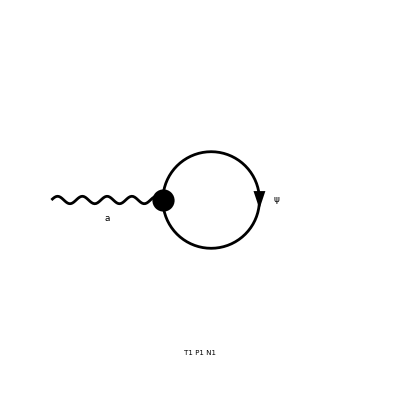

```mathematica
D1LA=diag[1,{V[1]},{}];
```

```mathematica
Amp1LA=D1LA//amp1L[{p1},{}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

in total: 0 Particles amplitudes

Part::partw: Part 2 of {} does not exist.

{(ⅈ e l^Lor1)/(4 π^4 (l^2-mP^2)),0}

```mathematica
Amp1LA//amp1LSimplify[{},{SMP["Delta"]}]
```

0

## One Loop (1->1)

## One Loop P->P

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

in total: 1 Particles insertion

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bd/cdcd.m, 0 diagrams

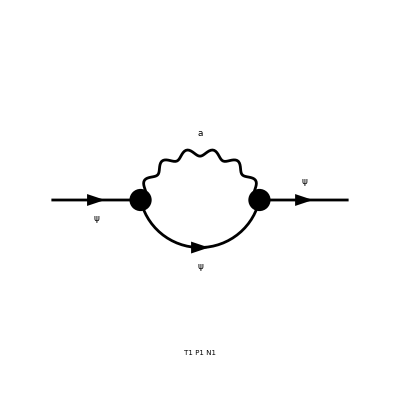

> Top. 1 ac/bc/0.m, 0 diagrams

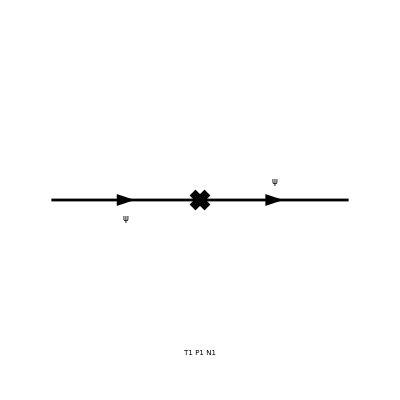

```mathematica
D1LPP=diag[1,{F[1]},{F[1]}];
```

```mathematica
Amp1LPP=D1LPP//amp1L[{p1},{p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ D e^2 γ·l)/(16 π^4 (l^2-mP^2).(l-p1)^2)+(ⅈ e^2 γ·l)/(8 π^4 (l^2-mP^2).(l-p1)^2)+(ⅈ D e^2 mP)/(16 π^4 (l^2-mP^2).(l-p1)^2)+(ⅈ e^2 mP (γ·l).(γ·p1))/(16 π^4 (l^2-mP^2).((l-p1)^2)^2)+(ⅈ e^2 mP (γ·p1).(γ·l))/(16 π^4 (l^2-mP^2).((l-p1)^2)^2)-(ⅈ e^2 mP (γ·l).(γ·p1) ξ_(V(1)))/(16 π^4 (l^2-mP^2).((l-p1)^2)^2)-(ⅈ e^2 mP (γ·p1).(γ·l) ξ_(V(1)))/(16 π^4 (l^2-mP^2).((l-p1)^2)^2)-(ⅈ e^2 γ·l l^2)/(16 π^4 (l^2-mP^2).((l-p1)^2)^2)+(ⅈ e^2 γ·p1 l^2)/(8 π^4 (l^2-mP^2).((l-p1)^2)^2)-(ⅈ e^2 mP l^2)/(16 π^4 (l^2-mP^2).((l-p1)^2)^2)+(ⅈ e^2 γ·l ξ_(V(1)) l^2)/(16 π^4 (l^2-mP^2).((l-p1)^2)^2)-(ⅈ e^2 γ·p1 ξ_(V(1)) l^2)/(8 π^4 (l^2-mP^2).((l-p1)^2)^2)+(ⅈ e^2 mP ξ_(V(1)) l^2)/(16 π^4 (l^2-mP^2).((l-p1)^2)^2)-(ⅈ e^2 γ·p1 (l·p1))/(8 π^4 (l^2-mP^2).((l-p1)^2)^2)+(ⅈ e^2 γ·p1 ξ_(V(1)) (l·p1))/(8 π^4 (l^2-mP^2).((l-p1)^2)^2)+(ⅈ e^2 γ·l p1^2)/(16 π^4 (l^2-mP^2).((l-p1)^2)^2)-(ⅈ e^2 mP p1^2)/(16 π^4 (l^2-mP^2).((l-p1)^2)^2)-(ⅈ e^2 γ·l ξ_(V(1)) p1^2)/(16 π^4 (l^2-mP^2).((l-p1)^2)^2)+(ⅈ e^2 mP ξ_(V(1)) p1^2)/(16 π^4 (l^2-mP^2).((l-p1)^2)^2),-ZmP ZP mP+mP+ZP γ·p1-γ·p1}

```mathematica
Amp1LPPDiv=Amp1LPP//amp1LSimplify[{ZP:> 1+Nd dP,ZmP:> 1+Nd dmP},{SMP["Delta"],dP, dmP}]
```

-dmP mP-dP mP+dP γ·p1-(3 Δ e^2 mP)/(8 π^2)-(Δ e^2 mP ξ_(V(1)))/(8 π^2)+(Δ e^2 ξ_(V(1)) γ·p1)/(8 π^2)

```mathematica
dsol[1]=Solve[SelectNotFree2[Amp1LPPDiv,p1]==0,dP]//Flatten//Simplify
dSave[dsol[1]];
```

{dP→-(Δ e^2 ξ_(V(1)))/(8 π^2)}

```mathematica
dsol[2]=Solve[SelectFree2[Amp1LPPDiv/.dSub[dmP],p1]==0,dmP]//Flatten//Simplify
dSave[dsol[2]];
```

{dmP→-(3 Δ e^2)/(8 π^2)}

## One Loop A->A

loading generic model file /home/raj/C_SM/ToySMat1Loop/models/QED/QED.gen

> $GenericMixing is OFF

generic model {./models/QED/QED} initialized

loading classes model file /home/raj/C_SM/ToySMat1Loop/models/QED/QED.mod

> 3 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 1 vertices

> 3 counterterms of order 1

classes model {./models/QED/QED} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

in total: 1 Particles insertion

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bd/cdcd.m, 0 diagrams

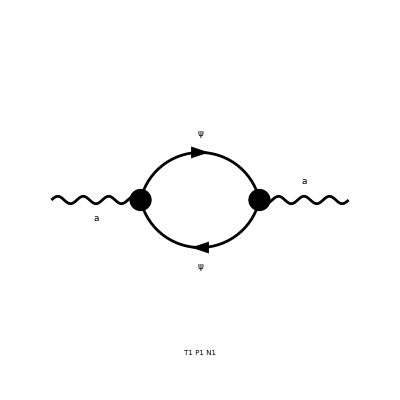

> Top. 1 ac/bc/0.m, 0 diagrams

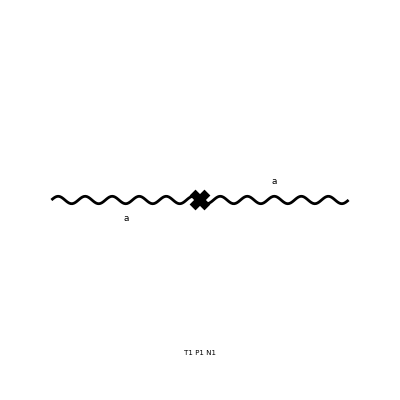

```mathematica
D1LAA=diag[1,{V[1]},{V[1]}];
```

```mathematica
Amp1LAA=D1LAA//amp1L[{p1},{p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{(ⅈ e^2 mP^2 g^Lor1Lor2)/(4 π^4 (l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^2 l^2 g^Lor1Lor2)/(4 π^4 (l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^2 g^Lor1Lor2 (l·p1))/(4 π^4 (l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^2 l^Lor1 l^Lor2)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^2 l^Lor2 p1^Lor1)/(4 π^4 (l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^2 l^Lor1 p1^Lor2)/(4 π^4 (l^2-mP^2).((l-p1)^2-mP^2)),-ⅈ (ⅈ (ZA-1) p1^Lor1 p1^Lor2-ⅈ p1^2 (ZA-1) g^Lor1Lor2)}

```mathematica
Amp1LAADiv=Amp1LAA//amp1LSimplify[{ZA:> 1+Nd dA},{SMP["Delta"],dA}]
```

-dA p1^2 g^Lor1Lor2+dA p1^Lor1 p1^Lor2-(Δ e^2 p1^2 g^Lor1Lor2)/(6 π^2)+(Δ e^2 p1^Lor1 p1^Lor2)/(6 π^2)

```mathematica
dsol[3]=Solve[SelectNotFree2[Amp1LAADiv/.dSub[dA],{SMP["Delta"],dA}]==0,dA]//Flatten//Simplify
dSave[dsol[3]];
```

{dA→-(Δ e^2)/(6 π^2)}

## One Loop (2->1)

## One Loop PP->A

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

in total: 1 Particles insertion

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 adbe/cf/dedfef.m, 0 diagrams

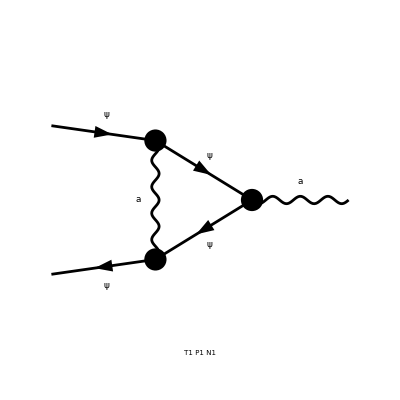

> Top. 1 adbd/cd/0.m, 0 diagrams

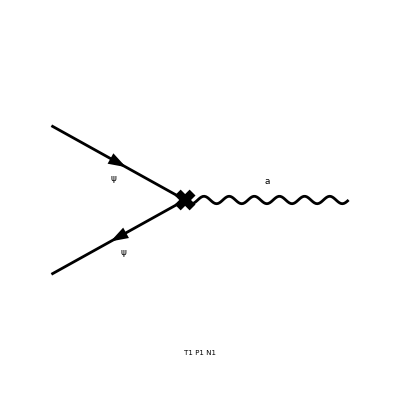

```mathematica
D1LPPA=diag[1,{F[1],-F[1]},{V[1]}];
```

```mathematica
Amp1LPPA=D1LPPA//amp1L[{p1,p1},{2p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ e^3 γ^Lor1 l^4)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 γ^Lor1 ξ_(V(1)) l^4)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ D e^3 mP^2 γ^Lor1)/(16 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 mP^2 γ^Lor1)/(8 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ D e^3 mP γ^Lor1.(γ·l))/(16 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 mP γ^Lor1.(γ·l))/(4 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ D e^3 mP γ^Lor1.(γ·p1))/(16 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 mP γ^Lor1.(γ·p1))/(4 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ D e^3 mP (γ·l).γ^Lor1)/(16 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 mP (γ·l).γ^Lor1)/(4 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ D e^3 mP (γ·p1).γ^Lor1)/(16 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 mP (γ·p1).γ^Lor1)/(4 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ D e^3 (γ·l).γ^Lor1.(γ·p1))/(16 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(3 ⅈ e^3 (γ·l).γ^Lor1.(γ·p1))/(8 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ D e^3 (γ·p1).γ^Lor1.(γ·l))/(16 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(3 ⅈ e^3 (γ·p1).γ^Lor1.(γ·l))/(8 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ D e^3 γ·l l^Lor1)/(8 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 γ·l l^Lor1)/(4 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 mP l^Lor1)/(2 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 mP^2 γ·l l^Lor1)/(8 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 mP (γ·p1).(γ·l) l^Lor1)/(4 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 mP^2 γ·l ξ_(V(1)) l^Lor1)/(8 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 mP (γ·p1).(γ·l) ξ_(V(1)) l^Lor1)/(4 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ D e^3 γ·p1 p1^Lor1)/(8 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 γ·p1 p1^Lor1)/(4 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ D e^3 γ^Lor1 l^2)/(16 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 γ^Lor1 l^2)/(8 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 mP^2 γ^Lor1 l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 mP γ^Lor1.(γ·l) l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 mP γ^Lor1.(γ·p1) l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 mP (γ·l).γ^Lor1 l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 mP (γ·p1).γ^Lor1 l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 γ^Lor1.(γ·p1).(γ·l) l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 (γ·l).(γ·p1).γ^Lor1 l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 mP^2 γ^Lor1 ξ_(V(1)) l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 mP γ^Lor1.(γ·l) ξ_(V(1)) l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 mP γ^Lor1.(γ·p1) ξ_(V(1)) l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 mP (γ·l).γ^Lor1 ξ_(V(1)) l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 mP (γ·p1).γ^Lor1 ξ_(V(1)) l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 γ^Lor1.(γ·p1).(γ·l) ξ_(V(1)) l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 (γ·l).(γ·p1).γ^Lor1 ξ_(V(1)) l^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 γ·p1 p1^Lor1 l^2)/(8 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 γ·p1 ξ_(V(1)) p1^Lor1 l^2)/(8 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 mP γ^Lor1.(γ·l) (l·p1))/(4 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 mP γ^Lor1.(γ·l) ξ_(V(1)) (l·p1))/(4 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 γ·l p1^Lor1 (l·p1))/(4 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 γ·l ξ_(V(1)) p1^Lor1 (l·p1))/(4 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ D e^3 γ^Lor1 p1^2)/(16 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 γ^Lor1 p1^2)/(8 π^4 l^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 γ·l l^Lor1 p1^2)/(8 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 γ·l ξ_(V(1)) l^Lor1 p1^2)/(8 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^3 γ^Lor1 l^2 p1^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^3 γ^Lor1 ξ_(V(1)) l^2 p1^2)/(16 π^4 (l^2)^2.((l+p1)^2-mP^2).((l-p1)^2-mP^2)),e γ^Lor1-e √ZA ZAPP ZP γ^Lor1}

```mathematica
Amp1LPPADiv=Amp1LPPA//amp1LSimplify[{ZAPP:> 1+Nd dAPP,ZP:> 1+Nd dP,ZA:> 1+Nd dA},{SMP["Delta"],dAPP,dP,dA}]
```

-1/2 dA e γ^Lor1-dAPP e γ^Lor1-dP e γ^Lor1-(Δ e^3 γ^Lor1 ξ_(V(1)))/(8 π^2)

```mathematica
dsol[4]=Solve[SelectNotFree2[Amp1LPPADiv/.dSub[dAPP],{SMP["Delta"],dAPP}]==0,dAPP]//Flatten//Simplify
dSave[dsol[4]];
```

{dAPP→(Δ e^2)/(12 π^2)}

## One Loop (2->2)

## One Loop SS->SS

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 1 Particles insertion

> Top. 8: 1 Particles insertion

> Top. 9: 2 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

in total: 4 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebf/cgdh/egehfgfh.m, 0 diagrams

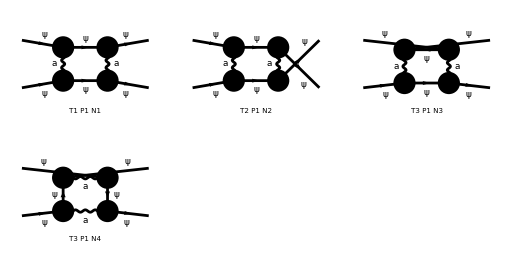

```mathematica
D1LPPPP=diag[1,{F[1],F[1]},{F[1],F[1]}];
```

```mathematica
Amp1LPPPP=D1LPPPP//amp1L[{p1,p1},{p1,p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 2 Particles amplitudes

in total: 4 Particles amplitudes

creating amplitudes at level(s) {Particles}

in total: 0 Particles amplitudes

{(ⅈ e^4 mP^2 ((γ·l).(γ·p1))^2 ξ_(V(1))^2)/(16 π^4 (l^2-mP^2).((l-p1)^2)^2.(l^2-mP^2).((l-p1)^2)^2)+596+(ⅈ e^4 γ·l (γ·p1).(γ·l).(γ·p1) ξ_(V(1)) p1^2)/(8 π^4 (l^2-mP^2).((l-p1)^2)^2.(l^2-mP^2).((l-p1)^2)^2)-(ⅈ e^4 mP (γ·p1).(γ·l).(γ·p1) ξ_(V(1)) p1^2)/(8 π^4 (l^2-mP^2).((l-p1)^2)^2.(l^2-mP^2).((l-p1)^2)^2),0}
 |  |  |  |

```mathematica
Amp1LPPPPDiv=Amp1LPPPP//amp1LSimplify[{},{SMP["Delta"]},True]
```

Current diagram:       Number of diagrams: 401

Time: 416.731 s

(mP γ^($AL($18389)).γ^Lor1 γ^($AL($18389)).(γ·p1).γ^Lor1 p1^2 Δ e^4)/(48 π^2 (mP^2-p1^2)^3)-(mP γ^($AL($18393)).γ^Lor1 γ^($AL($18393)).(γ·p1).γ^Lor1 p1^2 Δ e^4)/(12 π^2 (mP^2-p1^2)^3)+(mP γ^($AL($18395)).γ^Lor1 γ^($AL($18395)).(γ·p1).γ^Lor1 p1^2 Δ e^4)/(16 π^2 (mP^2-p1^2)^3)-(mP γ^($AL($19539)).γ^Lor2 γ^($AL($19539)).(γ·p1).γ^Lor2 p1^2 Δ e^4)/(48 π^2 (mP^2-p1^2)^3)+(mP γ^($AL($19543)).γ^Lor2 γ^($AL($19543)).(γ·p1).γ^Lor2 p1^2 Δ e^4)/(12 π^2 (mP^2-p1^2)^3)-(mP γ^($AL($19545)).γ^Lor2 γ^($AL($19545)).(γ·p1).γ^Lor2 p1^2 Δ e^4)/(16 π^2 (mP^2-p1^2)^3)-(mP γ^($AL($37656)).γ^Lor1 γ^($AL($37656)).(γ·p1).γ^Lor1 ξ_(V(1)) p1^2 Δ e^4)/(48 π^2 (mP^2-p1^2)^3)+(mP γ^($AL($37660)).γ^Lor1 γ^($AL($37660)).(γ·p1).γ^Lor1 ξ_(V(1)) p1^2 Δ e^4)/(12 π^2 (mP^2-p1^2)^3)-(mP γ^($AL($37662)).γ^Lor1 γ^($AL($37662)).(γ·p1).γ^Lor1 ξ_(V(1)) p1^2 Δ e^4)/(16 π^2 (mP^2-p1^2)^3)+(mP γ^($AL($38806)).γ^Lor2 γ^($AL($38806)).(γ·p1).γ^Lor2 ξ_(V(1)) p1^2 Δ e^4)/(48 π^2 (mP^2-p1^2)^3)-(mP γ^($AL($38810)).γ^Lor2 γ^($AL($38810)).(γ·p1).γ^Lor2 ξ_(V(1)) p1^2 Δ e^4)/(12 π^2 (mP^2-p1^2)^3)+(mP γ^($AL($38812)).γ^Lor2 γ^($AL($38812)).(γ·p1).γ^Lor2 ξ_(V(1)) p1^2 Δ e^4)/(16 π^2 (mP^2-p1^2)^3)-(mP^3 γ^($AL($18389)).γ^Lor1 γ^($AL($18389)).(γ·p1).γ^Lor1 Δ e^4)/(16 π^2 (mP^2-p1^2)^3)+(mP^3 γ^($AL($18393)).γ^Lor1 γ^($AL($18393)).(γ·p1).γ^Lor1 Δ e^4)/(8 π^2 (mP^2-p1^2)^3)-(mP^3 γ^($AL($18395)).γ^Lor1 γ^($AL($18395)).(γ·p1).γ^Lor1 Δ e^4)/(16 π^2 (mP^2-p1^2)^3)+(mP^3 γ^($AL($19539)).γ^Lor2 γ^($AL($19539)).(γ·p1).γ^Lor2 Δ e^4)/(16 π^2 (mP^2-p1^2)^3)-(mP^3 γ^($AL($19543)).γ^Lor2 γ^($AL($19543)).(γ·p1).γ^Lor2 Δ e^4)/(8 π^2 (mP^2-p1^2)^3)+(mP^3 γ^($AL($19545)).γ^Lor2 γ^($AL($19545)).(γ·p1).γ^Lor2 Δ e^4)/(16 π^2 (mP^2-p1^2)^3)+(mP^3 γ^($AL($37656)).γ^Lor1 γ^($AL($37656)).(γ·p1).γ^Lor1 ξ_(V(1)) Δ e^4)/(16 π^2 (mP^2-p1^2)^3)-(mP^3 γ^($AL($37660)).γ^Lor1 γ^($AL($37660)).(γ·p1).γ^Lor1 ξ_(V(1)) Δ e^4)/(8 π^2 (mP^2-p1^2)^3)+(mP^3 γ^($AL($37662)).γ^Lor1 γ^($AL($37662)).(γ·p1).γ^Lor1 ξ_(V(1)) Δ e^4)/(16 π^2 (mP^2-p1^2)^3)-(mP^3 γ^($AL($38806)).γ^Lor2 γ^($AL($38806)).(γ·p1).γ^Lor2 ξ_(V(1)) Δ e^4)/(16 π^2 (mP^2-p1^2)^3)+(mP^3 γ^($AL($38810)).γ^Lor2 γ^($AL($38810)).(γ·p1).γ^Lor2 ξ_(V(1)) Δ e^4)/(8 π^2 (mP^2-p1^2)^3)-(mP^3 γ^($AL($38812)).γ^Lor2 γ^($AL($38812)).(γ·p1).γ^Lor2 ξ_(V(1)) Δ e^4)/(16 π^2 (mP^2-p1^2)^3)

```mathematica
Amp1LPPPPDiv//FCCanonicalizeDummyIndices[#,LorentzIndexNames->{μ,ν,α,β,ρ,σ}]&//DiracSimplify[#,DiracSubstitute67->True]&
```

0

## One Loop SV->SV

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 1 Particles insertion

> Top. 8: 0 Particles insertions

> Top. 9: 1 Particles insertion

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/egehfgfh.m, 0 diagrams

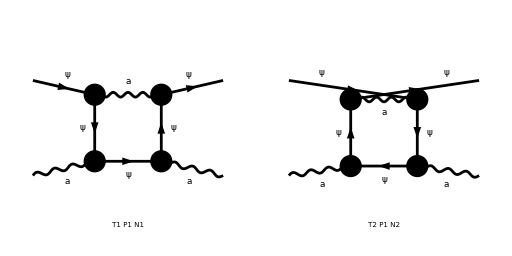

```mathematica
D1LPAPA=diag[1,{F[1],V[1]},{F[1],V[1]}];
```

```mathematica
Amp1LPAPA=D1LPAPA//amp1L[{p1,p1},{p1,p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

in total: 0 Particles amplitudes

{(ⅈ e^4 mP γ^Lor1.γ^Lor2 l^4)/(16 π^4 (l^2)^2.((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 γ^Lor1.γ^Lor2.(γ·p1) l^4)/(16 π^4 (l^2)^2.((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+588+(ⅈ e^4 γ^Lor2.γ^Lor1.(γ·l) ξ_(V(1)) (l·p1) p1^2)/(8 π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2)^2),0}
 |  |  |  |

```mathematica
Amp1LPAPADiv=Amp1LPAPA//amp1LSimplify[{},{SMP["Delta"]},True]
```

Current diagram:       Number of diagrams: 394

Time: 943.116 s

0

## One Loop VV->VV

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 2 Particles insertions

> Top. 9: 2 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

in total: 6 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebf/cgdh/egehfgfh.m, 0 diagrams

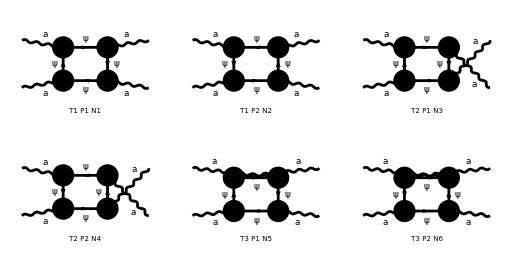

```mathematica
D1LAAAA=diag[1,{V[1],V[1]},{V[1],V[1]}];
```

```mathematica
Amp1LAAAA=D1LAAAA//amp1L[{p1,p1},{p1,p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

in total: 6 Particles amplitudes

creating amplitudes at level(s) {Particles}

in total: 0 Particles amplitudes

{(ⅈ e^4 g^Lor1Lor4 g^Lor2Lor3 l^4)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor3 g^Lor2Lor4 l^4)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor2 g^Lor3Lor4 l^4)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor2 g^Lor3Lor4 l^4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor4 g^Lor2Lor3 (l·p1)^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor3 g^Lor2Lor4 (l·p1)^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor2 g^Lor3Lor4 (l·p1)^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 g^Lor1Lor2 g^Lor3Lor4 (l·p1)^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^4 g^Lor1Lor4 g^Lor2Lor3)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^4 g^Lor1Lor3 g^Lor2Lor4)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 mP^4 g^Lor1Lor2 g^Lor3Lor4)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^4 g^Lor1Lor2 g^Lor3Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 mP^2 l^Lor1 l^Lor2 g^Lor3Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 p1^Lor1 p1^Lor2 g^Lor3Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 l^Lor1 g^Lor2Lor4 l^Lor3)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 l^Lor1 g^Lor2Lor4 l^Lor3)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 mP^2 p1^Lor1 g^Lor2Lor4 l^Lor3)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 mP^2 p1^Lor1 g^Lor2Lor4 l^Lor3)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 g^Lor1Lor4 l^Lor2 l^Lor3)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 g^Lor1Lor4 l^Lor2 l^Lor3)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 mP^2 g^Lor1Lor4 p1^Lor2 l^Lor3)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 mP^2 l^Lor1 g^Lor2Lor4 p1^Lor3)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 mP^2 g^Lor1Lor4 p1^Lor2 p1^Lor3)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 l^Lor1 g^Lor2Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 l^Lor1 g^Lor2Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 mP^2 p1^Lor1 g^Lor2Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 g^Lor1Lor3 l^Lor2 l^Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 g^Lor1Lor3 l^Lor2 l^Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 mP^2 g^Lor1Lor3 p1^Lor2 l^Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 mP^2 g^Lor1Lor3 p1^Lor2 l^Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 mP^2 g^Lor1Lor2 l^Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(4 ⅈ e^4 l^Lor1 l^Lor2 l^Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(8 ⅈ e^4 l^Lor1 l^Lor2 l^Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 p1^Lor1 l^Lor2 l^Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(4 ⅈ e^4 p1^Lor1 l^Lor2 l^Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 l^Lor1 p1^Lor2 l^Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(4 ⅈ e^4 l^Lor1 p1^Lor2 l^Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 p1^Lor1 p1^Lor2 l^Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 l^Lor1 l^Lor2 p1^Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 p1^Lor1 l^Lor2 p1^Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 l^Lor1 p1^Lor2 p1^Lor3 l^Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 mP^2 p1^Lor1 g^Lor2Lor3 p1^Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 mP^2 g^Lor1Lor3 l^Lor2 p1^Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 l^Lor1 l^Lor2 l^Lor3 p1^Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 p1^Lor1 l^Lor2 l^Lor3 p1^Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 l^Lor1 p1^Lor2 l^Lor3 p1^Lor4)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 g^Lor1Lor2 p1^Lor3 p1^Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 l^Lor1 l^Lor2 p1^Lor3 p1^Lor4)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 mP^2 g^Lor1Lor4 g^Lor2Lor3 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 mP^2 g^Lor1Lor3 g^Lor2Lor4 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 g^Lor1Lor2 g^Lor3Lor4 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 mP^2 g^Lor1Lor2 g^Lor3Lor4 l^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 l^Lor1 l^Lor2 g^Lor3Lor4 l^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 p1^Lor1 p1^Lor2 g^Lor3Lor4 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 l^Lor1 g^Lor2Lor4 l^Lor3 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 l^Lor1 g^Lor2Lor4 l^Lor3 l^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 p1^Lor1 g^Lor2Lor4 l^Lor3 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 p1^Lor1 g^Lor2Lor4 l^Lor3 l^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor4 l^Lor2 l^Lor3 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor4 l^Lor2 l^Lor3 l^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 g^Lor1Lor4 p1^Lor2 l^Lor3 l^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 l^Lor1 g^Lor2Lor4 p1^Lor3 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor4 p1^Lor2 p1^Lor3 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 l^Lor1 g^Lor2Lor3 l^Lor4 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 l^Lor1 g^Lor2Lor3 l^Lor4 l^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 p1^Lor1 g^Lor2Lor3 l^Lor4 l^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor3 l^Lor2 l^Lor4 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor3 l^Lor2 l^Lor4 l^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor3 p1^Lor2 l^Lor4 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 g^Lor1Lor3 p1^Lor2 l^Lor4 l^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 g^Lor1Lor2 l^Lor3 l^Lor4 l^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 p1^Lor1 g^Lor2Lor3 p1^Lor4 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor3 l^Lor2 p1^Lor4 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor2 p1^Lor3 p1^Lor4 l^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 g^Lor1Lor4 g^Lor2Lor3 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 g^Lor1Lor3 g^Lor2Lor4 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 mP^2 g^Lor1Lor2 g^Lor3Lor4 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 p1^Lor1 l^Lor2 g^Lor3Lor4 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 p1^Lor1 l^Lor2 g^Lor3Lor4 (l·p1))/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 l^Lor1 p1^Lor2 g^Lor3Lor4 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 l^Lor1 p1^Lor2 g^Lor3Lor4 (l·p1))/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 l^Lor1 g^Lor2Lor4 l^Lor3 (l·p1))/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 p1^Lor1 g^Lor2Lor4 l^Lor3 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 g^Lor1Lor4 l^Lor2 l^Lor3 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 g^Lor1Lor4 l^Lor2 l^Lor3 (l·p1))/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor4 p1^Lor2 l^Lor3 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 l^Lor1 g^Lor2Lor4 p1^Lor3 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor4 l^Lor2 p1^Lor3 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 l^Lor1 g^Lor2Lor3 l^Lor4 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 l^Lor1 g^Lor2Lor3 l^Lor4 (l·p1))/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 p1^Lor1 g^Lor2Lor3 l^Lor4 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 g^Lor1Lor3 l^Lor2 l^Lor4 (l·p1))/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor3 p1^Lor2 l^Lor4 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor2 p1^Lor3 l^Lor4 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 g^Lor1Lor2 p1^Lor3 l^Lor4 (l·p1))/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 l^Lor1 g^Lor2Lor3 p1^Lor4 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor3 l^Lor2 p1^Lor4 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor2 l^Lor3 p1^Lor4 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(2 ⅈ e^4 g^Lor1Lor2 l^Lor3 p1^Lor4 (l·p1))/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor4 g^Lor2Lor3 l^2 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor3 g^Lor2Lor4 l^2 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor2 g^Lor3Lor4 l^2 (l·p1))/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 g^Lor1Lor4 g^Lor2Lor3 p1^2)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 mP^2 g^Lor1Lor3 g^Lor2Lor4 p1^2)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 mP^2 g^Lor1Lor2 g^Lor3Lor4 p1^2)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 mP^2 g^Lor1Lor2 g^Lor3Lor4 p1^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 l^Lor1 l^Lor2 g^Lor3Lor4 p1^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 l^Lor1 l^Lor2 g^Lor3Lor4 p1^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 l^Lor1 g^Lor2Lor4 l^Lor3 p1^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 l^Lor1 g^Lor2Lor4 l^Lor3 p1^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor4 l^Lor2 l^Lor3 p1^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 l^Lor1 g^Lor2Lor3 l^Lor4 p1^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor3 l^Lor2 l^Lor4 p1^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor3 l^Lor2 l^Lor4 p1^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor2 l^Lor3 l^Lor4 p1^2)/(π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(2 ⅈ e^4 g^Lor1Lor2 l^Lor3 l^Lor4 p1^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor4 g^Lor2Lor3 l^2 p1^2)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^4 g^Lor1Lor3 g^Lor2Lor4 l^2 p1^2)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor2 g^Lor3Lor4 l^2 p1^2)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^4 g^Lor1Lor2 g^Lor3Lor4 l^2 p1^2)/(π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2)),0}

```mathematica
Amp1LAAAADiv=Amp1LAAAA//amp1LSimplify[{},{SMP["Delta"]},True]
```

Current diagram:       Number of diagrams: 120

Time: 79.0297 s

0

## Final answers

```mathematica
dvalues
```

{dP→-(Δ e^2 ξ_(V(1)))/(8 π^2),dmP→-(3 Δ e^2)/(8 π^2),dA→-(Δ e^2)/(6 π^2),dAPP→(Δ e^2)/(12 π^2)}

## Lamb shift

## Important functions

```mathematica
SimpAmp[sub__][exp_]:=((exp//temp1[sub]//temp2//ToPaVe[TID[#,l],l]&//PaXEvaluate[#,l,PaXImplicitPrefactor->1 ]&)/.{Epsilon->Epsilon/2})//FCHideEpsilon
```

PaXEvaluate uses d=4-2ϵ so we have to rescale the ϵ by factor of 2

```mathematica
p2denominator=(-(Pair[LorentzIndex[Lor1, D], Momentum[p1, D]]*Pair[LorentzIndex[Lor2, D], Momentum[p1, D]]) + Pair[LorentzIndex[Lor1, D], LorentzIndex[Lor2, D]]*Pair[Momentum[p1, D], Momentum[p1, D]]);
```

```mathematica
ExpandPbym[p1_,mP_][exp_]:=Module[{q},(exp/.{Pair[Momentum[p1,D],Momentum[p1,D]]->mP^2 q}//FullSimplify//Series[#,{q,0,1}]&//Normal)/.{ q->Pair[Momentum[p1,D],Momentum[p1,D]]/mP^2}/.{Pair[Momentum[p1,D],Momentum[p1,D]]->p1^2}]
```

## Amplitudes

```mathematica
D1LAA=diag[1,{V[1]},{V[1]}];
```

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

in total: 1 Particles insertion

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bd/cdcd.m, 0 diagrams

-Graphics-

> Top. 1 ac/bc/0.m, 0 diagrams

-Graphics-

```mathematica
Amp1LAA=D1LAA//amp1L[{p1},{p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{(ⅈ e^2 mP^2 g^Lor1Lor2)/(4 π^4 (l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^2 l^2 g^Lor1Lor2)/(4 π^4 (l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^2 g^Lor1Lor2 (l·p1))/(4 π^4 (l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ e^2 l^Lor1 l^Lor2)/(2 π^4 (l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^2 l^Lor2 p1^Lor1)/(4 π^4 (l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ e^2 l^Lor1 p1^Lor2)/(4 π^4 (l^2-mP^2).((l-p1)^2-mP^2)),-ⅈ (ⅈ (ZA-1) p1^Lor1 p1^Lor2-ⅈ p1^2 (ZA-1) g^Lor1Lor2)}

```mathematica
Amp1LAATotal=Amp1LAA//Total//SimpAmp[{ZA:> 1+Nd dA}]
```

1/(36 π^2 p1^4)(p1^Lor1 p1^Lor2-p1^2 g^Lor1Lor2) (36 π^2 dA p1^4+3 e^2 p1^4 log(μ^2/mP^2)+12 e^2 mP^2 p1^2+6 e^2 mP^2 √(-(p1^2 (4 mP^2-p1^2))) log((√(p1^2 (p1^2-4 mP^2))+2 mP^2-p1^2)/(2 mP^2))+3 e^2 p1^2 √(-(p1^2 (4 mP^2-p1^2))) log((√(p1^2 (p1^2-4 mP^2))+2 mP^2-p1^2)/(2 mP^2))+3 ℽ e^2 p1^4+5 e^2 p1^4-6 e^2 p1^4 log(4 π)-3 e^2 p1^4 log(π))+(Δ e^2 (p1^Lor1 p1^Lor2-p1^2 g^Lor1Lor2))/(6 π^2)

```mathematica
Π2=Amp1LAATotal/p2denominator//Simplify
```

-1/(36 π^2 p1^4)(p1^4 (36 π^2 dA+6 Δ e^2+3 e^2 log(μ^2/mP^2)+3 ℽ e^2+5 e^2-6 e^2 log(4 π)-3 e^2 log(π))+6 e^2 mP^2 √(p1^2 (p1^2-4 mP^2)) log((√(p1^2 (p1^2-4 mP^2))+2 mP^2-p1^2)/(2 mP^2))+3 p1^2 (e^2 √(p1^2 (p1^2-4 mP^2)) log((√(p1^2 (p1^2-4 mP^2))+2 mP^2-p1^2)/(2 mP^2))+4 e^2 mP^2))

Computing equation (16.48) of QFT and SM by Schwartz M.D. (2013)

```mathematica
Π2Finite=Π2/.dvalues//FullSimplify
```

-(e^2 (p1^4 (3 log(μ^2/mP^2)+3 ℽ+5-9 log(π)-6 log(4))+6 mP^2 √(p1^2 (p1^2-4 mP^2)) log((√(p1^2 (p1^2-4 mP^2))+2 mP^2-p1^2)/(2 mP^2))+3 p1^2 (√(p1^2 (p1^2-4 mP^2)) log((√(p1^2 (p1^2-4 mP^2))+2 mP^2-p1^2)/(2 mP^2))+4 mP^2)))/(36 π^2 p1^4)

Taking small momenta, large distance limit - equation (16.57) of QFT and SM by Schwartz M.D. (2013)

```mathematica
Π2FiniteSpLd=Π2Finite//ExpandPbym[p1,mP]
```

-(e^2 (log(μ^2/mP^2)+ℽ-3 log(π)-2 log(4)))/(12 π^2)-(e^2 p1^2)/(60 π^2 mP^2)

Choosing MS renormalization scheme where the finite part of the renormalized variable is zero.

```mathematica
Π2FiniteSpLdMS=Π2FiniteSpLd/.{ScaleMu->mP Exp[1/2(-EulerGamma+Log[16Pi^3])]}//FullSimplify
```

-(e^2 p1^2)/(60 π^2 mP^2)

### Potential in fourier space that after fourier transformation leads to potential with Coulomb and Uehling term. Equation (16.59) of QFT and SM by Schwartz M.D. (2013)

```mathematica
V=e^2/p1^2(1+Π2FiniteSpLdMS)//Expand
```

e^2/p1^2-e^4/(60 π^2 mP^2)